```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
k=Flatten[Import["./k1.dat"]]/197.33;
lam1=Flatten[Import["./lam1.dat"]];
lam2=Flatten[Import["./lam2.dat"]];
lam3=Flatten[Import["./lam3.dat"]];
lam1dl=lam1[[1;;Length[k]]]*k^-2;
lam2dl=lam2[[1;;Length[k]]];
lam3dl=lam3[[1;;Length[k]]]*k^2;
```

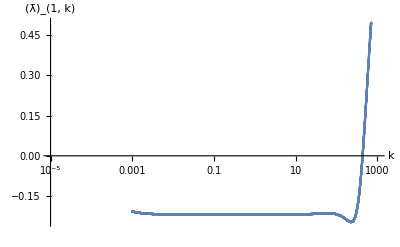

```mathematica
plotl1=ListLinePlot[Transpose[{k*197.33,lam1dl}],PlotRange->{{10^-5,1000},All},ScalingFunctions->{"Log",Automatic},AxesLabel->{"k","(λ̄)_(1, k)"}]
```

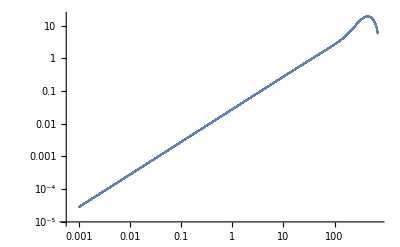

```mathematica
ListPlot[Transpose[{k*197.33,lam2dl}],ScalingFunctions->{"Log","Log"},PlotRange->All]
```

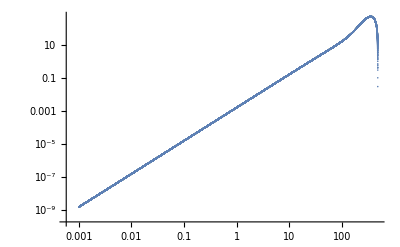

```mathematica
ListPlot[Transpose[{k*197.33,lam3dl}],ScalingFunctions->{"Log","Log"},PlotRange->All]
```